#### code below generates Figure 3A

```mathematica
xb5[T_,tl_,τ_]:=Reap[Do[ β=10^-8;  δ=1; μ=0.25;  s0=10^7; b=100;γxx[τx_,b_]:=b(τx+0.5)^0.8;
j[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
sol=NDSolve[{
D[s[t], t]==s0 j[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]== β γxx[τ,b] Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,v[t/;t≤0]==v0}, 
{s,v},{t,0,T}];
v0 =First@Evaluate[v[T]/.sol];
Sow[v0,a1];
,300],{a1}];
```

parasite equilibrium for τ = 3.2

```mathematica
T=4;tl=1;v0=1;
xx=xb5[T,tl,3.2]/.Null->Sequence[];
v0eq=Last[Flatten[xx,2][[1]]]
```

3.74751×10^8

parasite equilibrium for τ = 2

```mathematica
T=4;tl=1;v0=1;
xx=xb5[T,tl,2]/.Null->Sequence[];
v0eq=Last[Flatten[xx,2][[1]]]
```

2.84625×10^8

parasite equilibrium for τ = 1.8

```mathematica
T=4;tl=1;v0=1;
xx=xb5[T,tl,1.8]/.Null->Sequence[];
v0eq=Last[Flatten[xx,2][[1]]]
```

2.84543×10^8

parasite equilibrium for τ = 1

```mathematica
T=4;tl=1;v0=1;
xx=xb5[T,tl,1]/.Null->Sequence[];
v0eq=Last[Flatten[xx,2][[1]]]
```

1.83588×10^8

```mathematica
T=4;tl=1;v0=1;τx=2.8792617949379853;
xx=xb5[T,tl,τx]/.Null->Sequence[];
v0eq=Last[Flatten[xx,2][[1]]]
```

5.56239×10^8

```mathematica
(*set up vars and differential equations, for n strains*)
 Subscript[v0,1]=v0eq;
vars:=Table[{Subscript[v,j],Subscript[v,j],s},{j,n}];
eqns:={s'[t]==s0 j[t,tl]-μ s[t]-β *s[t] (Sum[Subscript[v,k][t] ,{k,n}]),Table[{Subscript[v,j]'[t]== β γxx[Subscript[τ,j],b] Exp[-μ Subscript[τ,j]]*s[t-Subscript[τ,j]]*Subscript[v,j][t-Subscript[τ,j]]-δ Subscript[v,j][t]},{j,n}]};
(*initial ICs*)
ics={Subscript[v,1][t/;t≤0]==Subscript[v0,1],s[t/;t≤0]==0};
τr={τ};τm={};

(*main loop*)
Monitor[Do[(*Subscript[τ,1]=3.2;*)Subscript[τ,1]=τx; (*Subscript[τ,1]=2;*)(*Subscript[τ,1]=1;*) v0m=1;β=10^-8;  δ=1; μ=0.25;  s0=10^7; b=100; nx=RandomInteger[{300,400}];
j[t_,tl_]:=If[0<t<tl,1/tl,0];Do[(*follows dynamics of n strains for nx seasons*)
sol=NDSolve[{Flatten[eqns],Flatten[Join[{s[t/;t≤0]==0},Flatten[Table[{Subscript[v,j][t/;t≤0]==Subscript[v0,j]},{j,n}]]]]},Flatten[vars],{t,0,T}][[1]];
Table[If[Evaluate[Subscript[v,j][T]/.sol]<1,Subscript[v0,j] =0,Subscript[v0,j] =Evaluate[Subscript[v,j][T]/.sol]],{j,n}];
If[Subscript[v0,n]<1,Break[]];,nx];
(*set τ for n=n+1 strains (mutates strain with highest density)*)
list=Table[Subscript[v0,j],{j,n}];
Subscript[τ,n+1]=Subscript[τ,First@Flatten[Position[list,Max[list]]]]+RandomVariate[NormalDistribution[0,0.1]];
τr=Append[τr,Subscript[τ,First@Flatten[Position[list,Max[list]]]]];
τm=Append[τm,Subscript[τ,n+1]];
(*set ic for n=n+1 strain*)
Subscript[v0,n+1]=1
,{n,10}],{n,τr,τm}]
```

```mathematica
τr
```

simulations 19-24 start with τ_1= 1

```mathematica
τr24=τr;
Export["smallrsims24.mx",τr24]
```

smallrsims24.mx

```mathematica
τr23=τr;
Export["smallrsims23.mx",τr23]
```

smallrsims23.mx

```mathematica
τr22=τr;
Export["smallrsims22.mx",τr22]
```

smallrsims22.mx

```mathematica
τr21=τr;
Export["smallrsims21.mx",τr21]
```

smallrsims21.mx

```mathematica
τr20=τr;
Export["smallrsims20.mx",τr20]
```

smallrsims20.mx

```mathematica
τr19=τr;
Export["smallrsims19.mx",τr19]
```

smallrsims19.mx

simulations 13-18 start with τ_1= 1.8

```mathematica
τr18=τr;
Export["smallrsims18.mx",τr18]
```

smallrsims18.mx

```mathematica
τr17=τr;
Export["smallrsims17.mx",τr17]
```

smallrsims17.mx

```mathematica
τr16=τr;
Export["smallrsims16.mx",τr16]
```

smallrsims16.mx

```mathematica
τr15=τr;
Export["smallrsims15.mx",τr15]
```

smallrsims15.mx

```mathematica
τr14=τr;
Export["smallrsims14.mx",τr14]
```

smallrsims14.mx

```mathematica
τr13=τr;
Export["smallrsims13.mx",τr13]
```

smallrsims13.mx

simulations 7-12 start with τ_1= 3.2

```mathematica
τr12=τr;
Export["smallrsims12.mx",τr12]
```

smallrsims12.mx

```mathematica
τr11=τr;
Export["smallrsims11.mx",τr11]
```

smallrsims11.mx

```mathematica
τr10=τr;
Export["smallrsims10.mx",τr10]
```

smallrsims10.mx

```mathematica
τr9=τr;
Export["smallrsims9.mx",τr9]
```

smallrsims9.mx

```mathematica
τr8=τr;
Export["smallrsims8.mx",τr8]
```

smallrsims8.mx

```mathematica
τr7=τr;
Export["smallrsims7.mx",τr7]
```

smallrsims7.mx

simulations 1-6 start with τ_1= 2

```mathematica
τr6=τr;
Export["smallrsims6.mx",τr6]
```

smallrsims6.mx

```mathematica
τr5=τr;
Export["smallrsims5.mx",τr5]
```

smallrsims5.mx

```mathematica
τr4=τr;
Export["smallrsims4.mx",τr4]
```

smallrsims4.mx

```mathematica
τr3=τr;
Export["smallrsims3.mx",τr3]
```

smallrsims3.mx

```mathematica
τr2=τr;
Export["smallrsims2.mx",τr2]
```

smallrsims2.mx

```mathematica
τr1=τr;
Export["smallrsims1.mx",τr1]
```

smallrsims1.mx

```mathematica
τr1=Import["smallrsims1.mx"];
τr2=Import["smallrsims2.mx"];
τr3=Import["smallrsims3.mx"];
τr4=Import["smallrsims4.mx"];
τr5=Import["smallrsims5.mx"];
τr6=Import["smallrsims6.mx"];
τr7=Import["smallrsims7.mx"];
τr8=Import["smallrsims8.mx"];
τr9=Import["smallrsims9.mx"];
τr10=Import["smallrsims10.mx"];
τr11=Import["smallrsims11.mx"];
τr12=Import["smallrsims12.mx"];
τr13=Import["smallrsims13.mx"];
τr14=Import["smallrsims14.mx"];
τr15=Import["smallrsims15.mx"];
τr16=Import["smallrsims16.mx"];
τr17=Import["smallrsims17.mx"];
τr18=Import["smallrsims18.mx"];
τr19=Import["smallrsims19.mx"];
τr20=Import["smallrsims20.mx"];
τr21=Import["smallrsims21.mx"];
τr22=Import["smallrsims22.mx"];
τr23=Import["smallrsims23.mx"];
τr24=Import["smallrsims24.mx"];
```

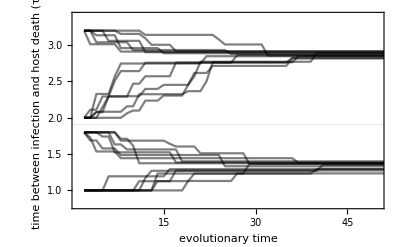

```mathematica
ListLinePlot[{τr1,τr2,τr3,τr4,τr5,τr6,τr7,τr8,τr9,τr10,τr11,τr12,τr13,τr14,τr15,τr16,τr17,τr18,τr19,τr20,τr21,τr22,τr23,τr24},Frame->True,FrameLabel->{{Style["time between infection\n and host death (τ)",16,FontFamily->"Helvetica"],None},{Style["evolutionary time",16,FontFamily->"Helvetica"],Style["small mutatation step size",16,FontFamily->"Helvetica"]}},PlotStyle->Directive[Black,Opacity[0.5]],PlotRange->{{1,50},{0.8,3.4}},GridLines->{None,{1.905}},GridLinesStyle->{Red,Thickness[0.004]},FrameStyle->14]
```

```mathematica
Export["smutsims.pdf",%]
```

smutsims.pdf

#### code below generates Figure 3B

simulations below are exactly the same as above, except that the mutation step size is bigger

```mathematica
xb5[T_,tl_,τ_]:=Reap[Do[ β=10^-8;  δ=1; μ=0.25; s0=10^7; b=100;γxx[τx_,b_]:=b(τx+0.5)^0.8;
j[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
sol=NDSolve[{
D[s[t], t]==s0 j[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]== β γxx[τ,b] Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,v[t/;t≤0]==v0}, 
{s,v},{t,0,T}];
v0 =First@Evaluate[v[T]/.sol];
Sow[v0,a1];
,300],{a1}];
```

parasite equilibrium for τ = 3.2

```mathematica
T=4;tl=1;v0=1;
xx=xb5[T,tl,3.2]/.Null->Sequence[];
v0eq=Last[Flatten[xx,2][[1]]]
```

3.74751×10^8

parasite equilibrium for τ = 2

```mathematica
T=4;tl=1;v0=1;
xx=xb5[T,tl,2]/.Null->Sequence[];
v0eq=Last[Flatten[xx,2][[1]]]
```

2.84625×10^8

parasite equilibrium for τ = 1.8

```mathematica
T=4;tl=1;v0=1;
xx=xb5[T,tl,1.8]/.Null->Sequence[];
v0eq=Last[Flatten[xx,2][[1]]]
```

2.84543×10^8

parasite equilibrium for τ = 1

```mathematica
T=4;tl=1;v0=1;
xx=xb5[T,tl,1]/.Null->Sequence[];
v0eq=Last[Flatten[xx,2][[1]]]
```

1.83588×10^8

```mathematica
(*set up vars and differential equations, for n strains*)
 Subscript[v0,1]=v0eq;
vars:=Table[{Subscript[v,j],Subscript[v,j],s},{j,n}];
eqns:={s'[t]==s0 j[t,tl]-μ s[t]-β *s[t] (Sum[Subscript[v,k][t] ,{k,n}]),Table[{Subscript[v,j]'[t]== β γxx[Subscript[τ,j],b] Exp[-μ Subscript[τ,j]]*s[t-Subscript[τ,j]]*Subscript[v,j][t-Subscript[τ,j]]-δ Subscript[v,j][t]},{j,n}]};
(*initial ICs*)
ics={Subscript[v,1][t/;t≤0]==Subscript[v0,1],s[t/;t≤0]==0};
τr={τ};τm={};

(*main loop*)
Monitor[Do[(*Subscript[τ,1]=1;*)Subscript[τ,1]=3.2; (*Subscript[τ,1]=1.8;*)(*Subscript[τ,1]=2;*) v0m=1;β=10^-8;  δ=1; μ=0.25;  s0=10^7; b=100; nx=RandomInteger[{300,400}];
j[t_,tl_]:=If[0<t<tl,1/tl,0];Do[(*follows dynamics of n strains for nx seasons*)
sol=NDSolve[{Flatten[eqns],Flatten[Join[{s[t/;t≤0]==0},Flatten[Table[{Subscript[v,j][t/;t≤0]==Subscript[v0,j]},{j,n}]]]]},Flatten[vars],{t,0,T}][[1]];
Table[If[Evaluate[Subscript[v,j][T]/.sol]<1,Subscript[v0,j] =0,Subscript[v0,j] =Evaluate[Subscript[v,j][T]/.sol]],{j,n}];
If[Subscript[v0,n]<1,Break[]];,nx];
(*set τ for n=n+1 strains (mutates strain with highest density)*)
list=Table[Subscript[v0,j],{j,n}];
Subscript[τ,n+1]=Subscript[τ,First@Flatten[Position[list,Max[list]]]]+RandomVariate[NormalDistribution[0,0.5]];
τr=Append[τr,Subscript[τ,First@Flatten[Position[list,Max[list]]]]];
τm=Append[τm,Subscript[τ,n+1]];
(*set ic for n=n+1 strain*)
Subscript[v0,n+1]=1
,{n,50}],{n,τr,τm}]
```

```mathematica
τr
```

{τ,3.2,3.13458,3.13458,3.13458,3.13458,3.13458,3.13458,3.13458,2.70413,2.70413,2.70413,2.70413,2.70413,2.70413,2.70413,2.70413,2.70413,2.70413,2.70413,2.70413,2.70413,2.70413,2.70413,2.70413,2.70413,2.70413,2.70413,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439,2.83439}

simulations 19-24 start with τ_1= 1

```mathematica
τr24=τr;
Export["bigrsims24.mx",τr24]
```

bigrsims24.mx

```mathematica
τr23=τr;
Export["bigrsims23.mx",τr23]
```

bigrsims23.mx

```mathematica
τr22=τr;
Export["bigrsims22.mx",τr22]
```

bigrsims22.mx

```mathematica
τr21=τr;
Export["bigrsims21.mx",τr21]
```

bigrsims21.mx

```mathematica
τr20=τr;
Export["bigrsims20.mx",τr20]
```

bigrsims20.mx

```mathematica
τr19=τr;
Export["bigrsims19.mx",τr19]
```

bigrsims19.mx

simulations 13-18 start with τ_1= 1.8

```mathematica
τr18=τr;
Export["bigrsims18.mx",τr18]
```

bigrsims18.mx

```mathematica
τr17=τr;
Export["bigrsims17.mx",τr17]
```

bigrsims17.mx

```mathematica
τr16=τr;
Export["bigrsims16.mx",τr16]
```

bigrsims16.mx

```mathematica
τr15=τr;
Export["bigrsims15.mx",τr15]
```

bigrsims15.mx

```mathematica
τr14=τr;
Export["bigrsims14.mx",τr14]
```

bigrsims14.mx

```mathematica
τr13=τr;
Export["bigrsims13.mx",τr13]
```

bigrsims13.mx

simulations 7-12 start with τ_1= 3.2

```mathematica
τr12=τr;
Export["bigrsims12.mx",τr12]
```

bigrsims12.mx

```mathematica
τr11=τr;
Export["bigrsims11.mx",τr11]
```

bigrsims11.mx

```mathematica
τr10=τr;
Export["bigrsims10.mx",τr10]
```

bigrsims10.mx

```mathematica
τr9=τr;
Export["bigrsims9.mx",τr9]
```

bigrsims9.mx

```mathematica
τr8=τr;
Export["bigrsims8.mx",τr8]
```

bigrsims8.mx

```mathematica
τr7=τr;
Export["bigrsims7.mx",τr7]
```

bigrsims7.mx

simulations 1-6 start with τ_1= 2

```mathematica
τr6=τr;
Export["bigrsims6.mx",τr6]
```

bigrsims6.mx

```mathematica
τr5=τr;
Export["bigrsims5.mx",τr5]
```

bigrsims5.mx

```mathematica
τr4=τr;
Export["bigrsims4.mx",τr4]
```

bigrsims4.mx

```mathematica
τr3=τr;
Export["bigrsims3.mx",τr3]
```

bigrsims3.mx

```mathematica
τr2=τr;
Export["bigrsims2.mx",τr2]
```

bigrsims2.mx

```mathematica
τr1=τr;
Export["bigrsims1.mx",τr1]
```

bigrsims1.mx

```mathematica
τr1=Import["bigrsims1.mx"];
τr2=Import["bigrsims2.mx"];
τr3=Import["bigrsims3.mx"];
τr4=Import["bigrsims4.mx"];
τr5=Import["bigrsims5.mx"];
τr6=Import["bigrsims6.mx"];
τr7=Import["bigrsims7.mx"];
τr8=Import["bigrsims8.mx"];
τr9=Import["bigrsims9.mx"];
τr10=Import["bigrsims10.mx"];
τr11=Import["bigrsims11.mx"];
τr12=Import["bigrsims12.mx"];
τr13=Import["bigrsims13.mx"];
τr14=Import["bigrsims14.mx"];
τr15=Import["bigrsims15.mx"];
τr16=Import["bigrsims16.mx"];
τr17=Import["bigrsims17.mx"];
τr18=Import["bigrsims18.mx"];
τr19=Import["bigrsims19.mx"];
τr20=Import["bigrsims20.mx"];
τr21=Import["bigrsims21.mx"];
τr22=Import["bigrsims22.mx"];
τr23=Import["bigrsims23.mx"];
τr24=Import["bigrsims24.mx"];
```

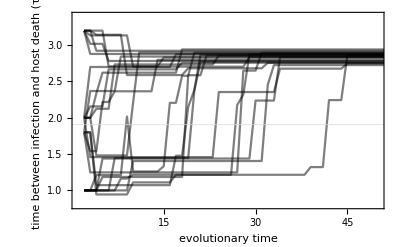

```mathematica
nes=ListLinePlot[{τr1,τr2,τr3,τr4,τr5,τr6,τr7,τr8,τr9,τr10,τr11,τr12,τr13,τr14,τr15,τr16,τr18,τr19,τr20,τr21,τr22,τr23,τr24},Frame->True,FrameLabel->{{Style["time between infection\n and host death (τ)",16,FontFamily->"Helvetica"],None},{Style["evolutionary time",16,FontFamily->"Helvetica"],Style["large mutatation step size",16,FontFamily->"Helvetica"]}},FrameStyle->14,PlotStyle->Directive[Black,Opacity[0.5]],PlotRange->{{1,50},{0.8,3.4}},GridLines->{None,{1.905}},GridLinesStyle->{Red,Thickness[0.004]}]
```

```mathematica
Export["bmutsims.pdf",%]
```

bmutsims.pdf

#### code below generates Figure 6B

```mathematica
ClearAll["Global`*"]
vcr[T_,tl_,τ_,β_,δ_,μ_, b_,σ_,ρ_,0]:=vcr[T,tl,τ,β,δ,μ,b,σ,ρ,0]=1;
j1[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
γxx[τx_,b_]:=b(τx+0.5)^0.8;
vcr[T_,tl_,τ_,β_,δ_,μ_, b_,σ_,ρ_,n_]:=vcr[T,tl,τ,β,δ,μ,b,σ,ρ,n]=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,b,σ,ρ,n-1]* j1[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,b,σ,ρ,n-1]}, 
{v},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
vcr[T,tl,τ,β,δ,μ, b,σ,ρ,n] =First@Evaluate[v[T]/.sol])
sc[T_,tl_,τ_,β_,δ_,μ_, b_,σ_,ρ_,0]:=sc[T,tl,τ,β,δ,μ,b,σ,ρ,0]=10^7;
sc[T_,tl_,τ_,β_,δ_,μ_, b_,σ_,ρ_,n_]:=sc[T,tl,τ,β,δ,μ,b,σ,ρ,n]=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,b,σ,ρ,n-1]* j1[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,b,σ,ρ,n-1]}, 
{s},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
sc[T,tl,τ,β,δ,μ, b,σ,ρ,n]=First@Evaluate[(σ s[T]/(1+ρ s[T]))/.sol])
```

```mathematica
(*set up vars and differential equations, for n strains*)
v0eq=vcr[4,1,2,10^-7,1,0.25,75, 200,0.0001,300];
 Subscript[v0,1]=v0eq;
vars:=Table[{Subscript[v,j],s},{j,n}];
eqns:={s'[t]==s0 j1[t,tl]-μ s[t]-β*s[t] (Sum[Subscript[v,k][t] ,{k,n}]),Table[{Subscript[v,j]'[t]== β γxx[Subscript[τ,j],b]Exp[-μ Subscript[τ,j]]*s[t-Subscript[τ,j]]*Subscript[v,j][t-Subscript[τ,j]]-δ Subscript[v,j][t]},{j,n}]};
(*initial ICs*)
ics={Subscript[v,1][t/;t≤0]==Subscript[v0,1],s[t/;t≤0]==0};
τr={τ};τm={};

(*main loop*)
Monitor[Do[(*Subscript[τ,1]=2;Subscript[τ,1]=1.85;Subscript[τ,1]=3.1;*) Subscript[τ,1]=0.75; v10m=1; s0=sc[4,1,2,10^-7,1,0.25,75, 200,0.0001,300]; b=75; β=10^-7;  δ=1; μ=0.25;  tl=1; T=4; σ=200; α=0.0001; nx=RandomInteger[{1000,1100}];Do[(*follows dynamics of n strains for nx seasons*)
sol=NDSolve[{Flatten[eqns],Flatten[Join[{s[t/;t≤0]==0},Flatten[Table[{Subscript[v,j][t/;t≤0]==Subscript[v0,j]},{j,n}]]]]},Flatten[vars],{t,0,T}][[1]];
Table[If[Evaluate[Subscript[v,j][T]/.sol]<1,Subscript[v0,j] =0,Subscript[v0,j] =Evaluate[Subscript[v,j][T]/.sol]],{j,n}];
s0 = Evaluate[σ s[T]/(1+ α s[T])/.sol];
If[Subscript[v0,n]<1,Break[]];,nx];
(*set τ for n=n+1 strains (mutates strain with highest density)*)
list=Table[Subscript[v0,j],{j,n}];
Subscript[τ,n+1]=Subscript[τ,First@Flatten[Position[list,Max[list]]]]+RandomVariate[NormalDistribution[0,0.1]];
τr=Append[τr,Subscript[τ,First@Flatten[Position[list,Max[list]]]]];
τm=Append[τm,Subscript[τ,n+1]];
(*set ic for n=n+1 strain*)
Subscript[v0,n+1]=1
,{n,50}],{n,τr,τm}]
```

```mathematica
τr
```

```mathematica
τm
```

starting τ = 3.1 below

```mathematica
τr15=τr;
τm15=τm;
Export["trcsims15.mx",τr15]
Export["tmcsims15.mx",τm15]
```

trcsims15.mx

tmcsims15.mx

```mathematica
τr14=τr;
τm14=τm;
Export["trcsims14.mx",τr14]
Export["tmcsims14.mx",τm14]
```

trcsims14.mx

tmcsims14.mx

```mathematica
τr13=τr;
τm13=τm;
Export["trcsims13.mx",τr13]
Export["tmcsims13.mx",τm13]
```

trcsims13.mx

tmcsims13.mx

```mathematica
τr12=τr;
τm12=τm;
Export["trcsims12.mx",τr12]
Export["tmcsims12.mx",τm12]
```

trcsims12.mx

tmcsims12.mx

```mathematica
τr11=τr;
τm11=τm;
Export["trcsims11.mx",τr11]
Export["tmcsims11.mx",τm11]
```

trcsims11.mx

tmcsims11.mx

starting τ = 3.1 above and starting τ = 1.85 below

```mathematica
τr10=τr;
τm10=τm;
Export["trcsims10.mx",τr10]
Export["tmcsims10.mx",τm10]
```

trcsims10.mx

tmcsims10.mx

```mathematica
τr9=τr;
τm9=τm;
Export["trcsims9.mx",τr9]
Export["tmcsims9.mx",τm9]
```

trcsims9.mx

tmcsims9.mx

```mathematica
τr8=τr;
τm8=τm;
Export["trcsims8.mx",τr8]
Export["tmcsims8.mx",τm8]
```

trcsims8.mx

tmcsims8.mx

```mathematica
τr7=τr;
τm7=τm;
Export["trcsims7.mx",τr7]
Export["tmcsims7.mx",τm7]
```

trcsims7.mx

tmcsims7.mx

```mathematica
τr6=τr;
τm6=τm;
Export["trcsims6.mx",τr6]
Export["tmcsims6.mx",τm6]
```

trcsims6.mx

tmcsims6.mx

starting τ = 1.85 above and starting τ = 2 below

```mathematica
τr5=τr;
τm5=τm;
Export["trcsims5.mx",τr5]
Export["tmcsims5.mx",τm5]
```

trcsims5.mx

tmcsims5.mx

```mathematica
τr4=τr;
τm4=τm;
Export["trcsims4.mx",τr4]
Export["tmcsims4.mx",τm4]
```

trcsims4.mx

tmcsims4.mx

```mathematica
τr3=τr;
τm3=τm;
Export["trcsims3.mx",τr3]
Export["tmcsims3.mx",τm3]
```

trcsims3.mx

tmcsims3.mx

```mathematica
τr2=τr;
τm2=τm;
Export["trcsims2.mx",τr2]
Export["tmcsims2.mx",τm2]
```

trcsims2.mx

tmcsims2.mx

```mathematica
τr1=τr;
τm1=τm;
Export["trcsims1.mx",τr1]
Export["tmcsims1.mx",τm1]
```

trcsims1.mx

tmcsims1.mx

```mathematica
τr1=Import["trcsims1.mx"];
τr2=Import["trcsims2.mx"];
τr3=Import["trcsims3.mx"];
τr4=Import["trcsims4.mx"];
τr5=Import["trcsims5.mx"];
τr6=Import["trcsims6.mx"];
τr7=Import["trcsims7.mx"];
τr8=Import["trcsims8.mx"];
τr9=Import["trcsims9.mx"];
τr10=Import["trcsims10.mx"];
τr11=Import["trcsims11.mx"];
τr12=Import["trcsims12.mx"];
τr13=Import["trcsims13.mx"];
τr14=Import["trcsims14.mx"];
τr15=Import["trcsims15.mx"];
```

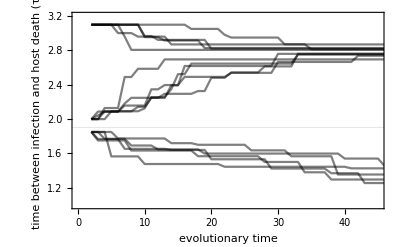

```mathematica
ListLinePlot[{τr1,τr2,τr3,τr4,τr5,τr6,τr7,τr8,τr9,τr10,τr11,τr12,τr13,τr14,τr15},Frame->True,FrameLabel->{{Style["time between infection\n and host death (τ)",16,FontFamily->"Helvetica"],None},{Style["evolutionary time",16,FontFamily->"Helvetica"],Style["",16,FontFamily->"Helvetica"]}},PlotStyle->Directive[Black,Opacity[0.5]],PlotRange->{{0,45},{1,3.2}},FrameStyle->14,GridLines->{None,{1.905}},GridLinesStyle->{Red,Thickness[0.004]}]
```

```mathematica
Export["periodicsims.pdf",%]
```

periodicsims.pdf

note that we don’t start the simulation with very high virulence (short τ) as the dynamics cycle in this region of the parameter space and simulations take too long to complete